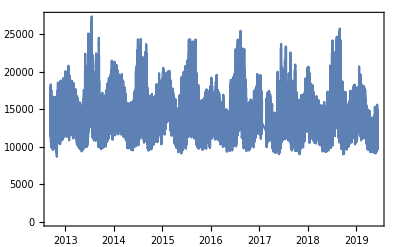

```mathematica
DateListPlot[neISOLoad]
```

```mathematica
toDate[dates_List] := Map[toDate, dates]
toDate[dateObject_DateObject] := DateObject[DateValue[dateObject, {"Year", "Month", "Day"}]];
```

```mathematica
loadDataDateTime
```

```mathematica
regroupdata[objects_] := DateListPlot[TimeSeries @ Map[
	{#["DateTime"], #["MWh"]} &,
	objects
]]


allplots = GroupBy[
	Normal[loadDataDateTime], 
	toDate[#DateTime] &,
regroupdata
];
```

```mathematica
Manipulate[
allplots[date],
{date, Keys[allplots]}
]
```